```mathematica
ComplexExpand[ (p + I q) (x + I y) + a x - I b y]
```

a x+p x-q y+ⅈ (q x-b y+p y)

```mathematica
D[a x+p x-q y,x] - D[q x-b y+p y,y]
```

a+b

```mathematica
ComplexExpand[(X' + I Y')((p + I q) (X + I Y) +a X - I b Y)]
```

a X X'+p X X'-q Y X'-q X Y'+b Y Y'-p Y Y'+ⅈ (q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y')

```mathematica
EqPol =Simplify[(q X X'-b Y X'+p Y X'+a X Y'+p X Y'-q Y Y')/.
{X' -> D[r[θ] Cos[θ],θ], Y' -> D[r[θ]Sin[θ],θ], X -> r[θ] Cos[θ], Y->r[θ]Sin[θ]}]
```

1/2 r[θ] (r[θ] (a+b+(a-b+2 p) Cos[2 θ]-2 q Sin[2 θ])+(2 q Cos[2 θ]+(a-b+2 p) Sin[2 θ]) r'[θ])

```mathematica
lr=f[θ]/.DSolve[( (a+b+(a-b+2 p) Cos[2 θ]-2 q Sin[2 θ])+(2 q Cos[2 θ]+(a-b+2 p) Sin[2 θ])f'[θ])==0,f[θ],θ][[1]]
```

C[1]-(2 (a+b) ArcTanh[(-a+b-2 p+2 q Tan[θ])/(√(a^2-2 a b+b^2+4 a p-4 b p+4 p^2+4 q^2))]+√(a^2-2 a b+b^2+4 a p-4 b p+4 p^2+4 q^2) Log[2 q Cos[2 θ]+(a-b+2 p) Sin[2 θ]])/(2 √(a^2+b^2-2 a (b-2 p)-4 b p+4 (p^2+q^2)))

```mathematica
q2sol ={C[1]->0,q^2 ->1/4(S - (a^2+b^2-2 a (b-2 p)-4 b p+4 (p^2)))};
```

```mathematica
lrS =lr/.q2sol//Simplify
```

-((a+b) ArcTanh[(-a+b-2 p+2 q Tan[θ])/(√S)])/(√S)-1/2 Log[2 q Cos[2 θ]+(a-b+2 p) Sin[2 θ]]

```mathematica
S-> a^2+b^2-2 a (b-2 p)-4 b p+4 (p^2+q^2)
```

S→a^2+b^2-2 a (b-2 p)-4 b p+4 (p^2+q^2)

```mathematica
TrigToExp[ArcTanh[x]]
```

-1/2 Log[1-x]+1/2 Log[1+x]

```mathematica
collectLog[expr_]:=Module[{rule1,rule2,a,b,x},
rule1=Log[a_]+Log[b_]:>Log[a*b];
rule2=x_*Log[a_]:>Log[a^x];
rule3 = x_ ArcTanh[a_] :> Log[(1 + a)^(x/2) (1-a)^(-x/2)];
expr//.{rule1,rule2,rule3}
];
```

```mathematica
rS = Simplify[collectLog[lrS]/.{Log->Identity, b-> -c-a, p-> (-2a - c-H)/2, S-> B^2},B>0]
```

((B-H-2 q Tan[θ])^(-c/(2 B)) (B+H+2 q Tan[θ])^(c/(2 B)))/(√(2 q Cos[2 θ]-H Sin[2 θ]))

```mathematica
Simplify[a^2+b^2-2 a (b-2 p)-4 b p+4 p^2] + 4 q^2
```

(a-b+2 p)^2+4 q^2

```mathematica
H->-a + b -2 p
```

H→-a+b-2 p

```mathematica
(*&&B=c/(2 n ),\\
&&H=-c\cos\beta;\\
&&q= \oh c\sin\beta;\\
&&p=-a-c (1-\cos\beta)/2*)
```

```mathematica
H = -B Cos[β];
q = 1/2 B Sin[β];
A =Simplify[Cos[θ](1 -Sin[β]Simplify[ (B + H+2 q Tan[θ])/B/Sin[β]])]
```

Cos[β+θ]

```mathematica
A1 =Simplify[ 2 Cos[θ] - A]
```

2 Cos[θ]-Cos[β+θ]

```mathematica
Rat = FullSimplify[(2 q/B Cos[2 θ]-H/B Sin[2 θ]),{θ>0, β>0}]
```

Sin[β+2 θ]

```mathematica
R[β_,θ_,n_] :=Evaluate[FullSimplify[A1^(1-n ) A^n/ Sqrt[Rat]]]
```

```mathematica
R[β,θ,n]
```

((2 Cos[θ]-Cos[β+θ])^(1-n) Cos[β+θ]^n)/(√Sin[β+2 θ])

```mathematica
(*OK[β_,θ_] :=Solve[-Pi/2 -β<θ< Pi/2 -β && -β/2 <θ < Pi/2 - β/2 && -Pi/2 <θ < Pi/2, θ]; *)
```

```mathematica
Lims[β_] := {Max[{-Pi/2 -β,-β/2,-Pi/2}],Min[{Pi/2 -β,Pi/2 - β/2,Pi/2}]}
```

```mathematica
Lims[0.25 Pi]
```

{-0.392699,0.785398}

```mathematica
PlotRadPolar[β_?NumericQ, nn_] :=
Show[
MapThread[
ParametricPlot[
{ReIm[R[β,θ,#1]Exp[I θ]],ReIm[R[β,θ,#1]Exp[-I θ]]},{θ,0,Pi/2-β},
PlotLabel->Row[{"Quantized Vortex Sheets for ",TraditionalForm[Symbol["β"]==β]}],
AspectRatio->1,
PlotStyle->#2,
PlotLabels->Placed[TraditionalForm[Symbol["n"]==#1],Above]
]&,{nn,Take[ColorData[97,"ColorList"],Length[nn]]}
]
]
```

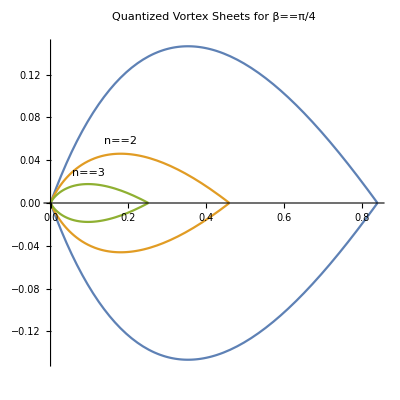

```mathematica
PlotRadPolar[Pi/4,{1,2,3}]
```

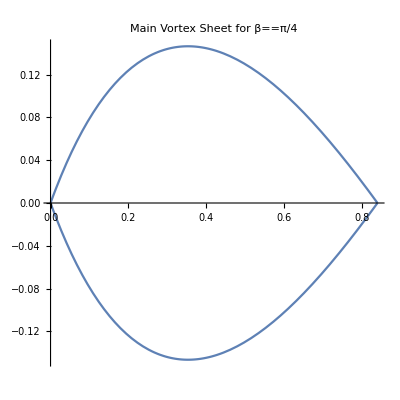

```mathematica
Module[{ X,Y,β=Pi/4, n=1},
ParametricPlot[
{X,Y}=ReIm[R[β,θ,n]Exp[I θ]];
{{X,Y},{X,-Y}},{θ,0,Pi/2-β}, 
AspectRatio->1,
PlotLabel->Row[{"Main Vortex Sheet for ",TraditionalForm[Symbol["β"]==β]}]
]]
```